```mathematica
(*srezdata = Cases[data,{_ (*t_ /; (t>=0.03)&&(t<0.04)*),x_ /; x==a  ,_,_}/.a-> 0.40];
tdata = srezdata⟦All, 1⟧;
udata = srezdata⟦All, 3⟧;
listTU ={tdata,udata}^ᵀ;
ListLinePlot[listTU]*)
(*ListContourPlot[data⟦All,1;;3⟧]
ListContourPlot[data⟦All,{1,2,4}⟧]*)
Module[{data},
data =Import["C:/Users/Daria/Desktop/биофиз/brusselator/sravn/bruseplb15k.dat", "Table"];
ListPlot3D[data⟦All,1;;3⟧] ;
ListPlot3D[data⟦All,{1,2,4}⟧]
]
```

-Graphics-

-Graphics-

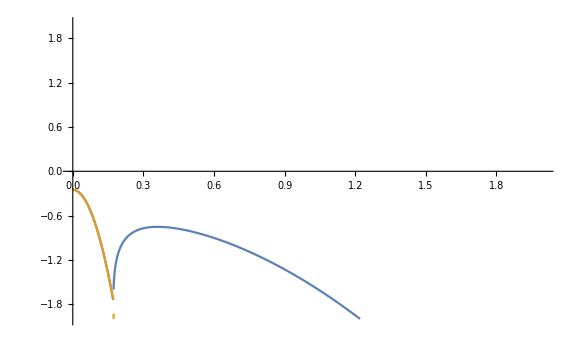

```mathematica
Assuming[{k∈Reals,k>0},
Block[{B=1.5,A=1,Du=1,Dv=100},
p1[k_] := 0.5*(B-1-A^2-(Du+Dv)k^2+Sqrt[(B-1-A^2-(Du-Dv)k^2)^2-4 A^2 B]);
p2[k_] := 0.5*(B-1-A^2-(Du+Dv)k^2-Sqrt[(B-1-A^2-(Du-Dv)k^2)^2-4 A^2 B]);
realp1[k_] :=Re@p1[k];
realp2[k_] :=Re@p2[k];
(*Export["C:/Users/Daria/Desktop/биофиз/brusselator/dispersB=3.png",Plot[{realp1[k], realp2[k]},{k,0,2}, PlotRange->{{0,2}, {-2,2}}]]; *)
Show[Plot[{ realp1[k],realp2[k]},{k,0,2}, PlotRange->{{0,2}, {-2,2}}, ImageSize->Large]]
]
]
```